# Supplementary tensors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<ITensor`
<<CTensor`
<<CITensor`
<<CIITensor`
<<CIIITensor`
<<CIIIITensor`
<<ETensor`
<<CETensor`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## ITensor

-Graphics-

The trimmed mean evaluation time is 0.0000086675 seconds

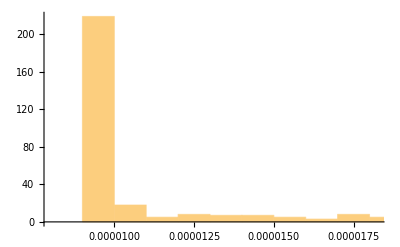

```mathematica
Table[Timing[ITensor[{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0000361825 seconds

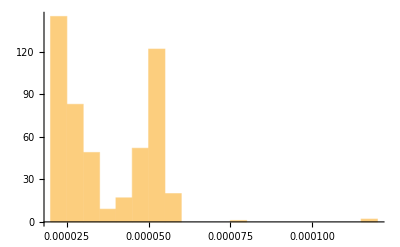

```mathematica
Table[Timing[ITensor[{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000598332 seconds

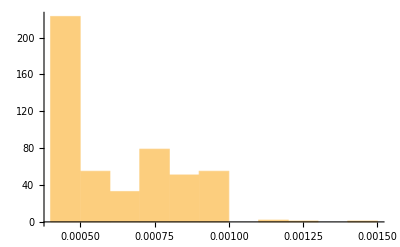

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000346633 seconds

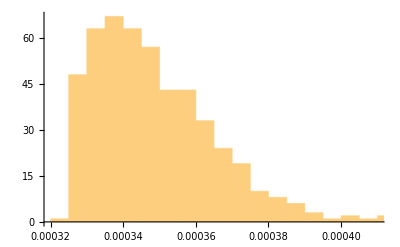

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0027979 seconds

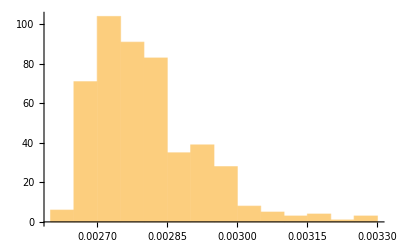

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0340396 seconds

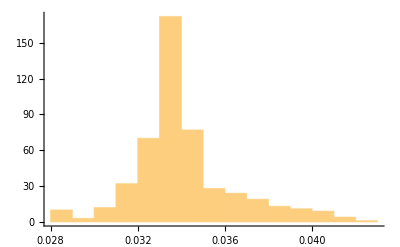

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.49704 seconds

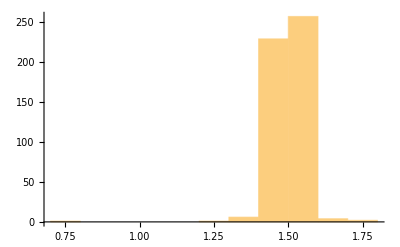

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5,r6,s6}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## CTensor

-Graphics-

The trimmed mean evaluation time is 0.0000077775 seconds

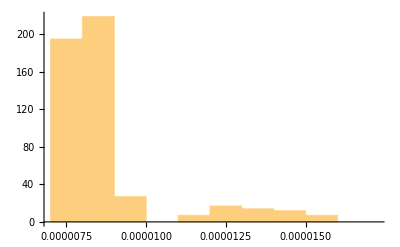

```mathematica
Table[Timing[CTensor[{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000476925 seconds

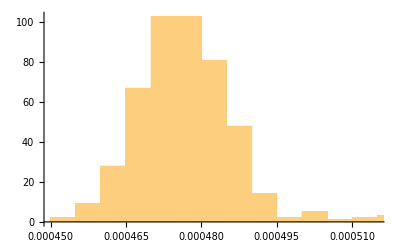

```mathematica
Table[Timing[CTensor[{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000655163 seconds

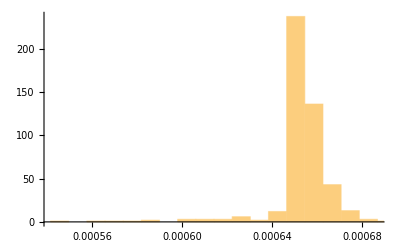

```mathematica
Table[Timing[CTensor[{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00526628 seconds

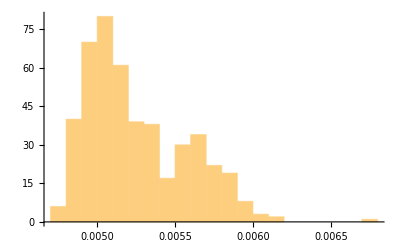

```mathematica
Table[Timing[CTensor[{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0951558 seconds

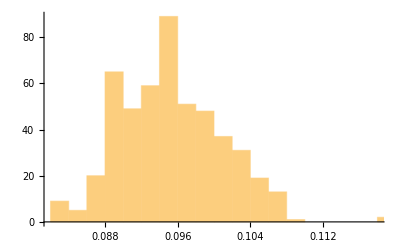

```mathematica
Table[Timing[CTensor[{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 2.22279 seconds

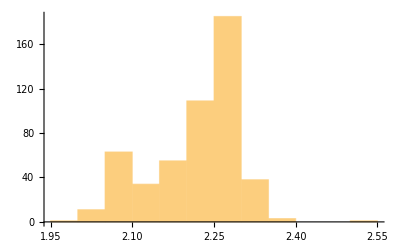

```mathematica
Table[Timing[CTensor[{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## CITensor

-Graphics-

The trimmed mean evaluation time is 0.000017225 seconds

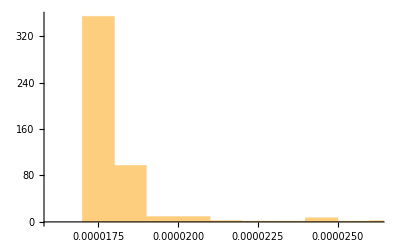

```mathematica
Table[Timing[CITensor[{μ,ν},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00080583 seconds

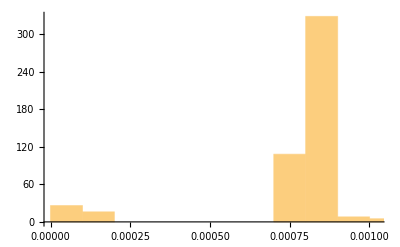

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00115837 seconds

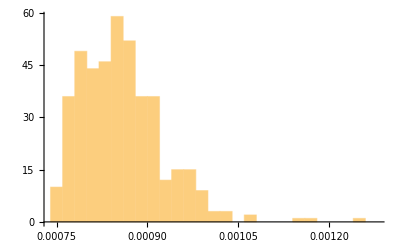

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0121642 seconds

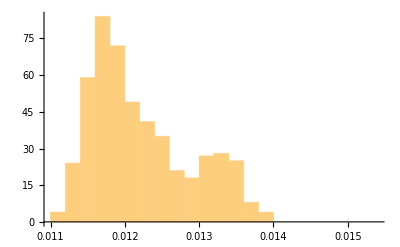

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.222694 seconds

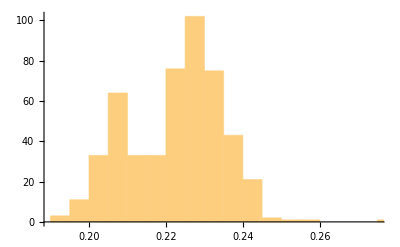

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 6.03742 seconds

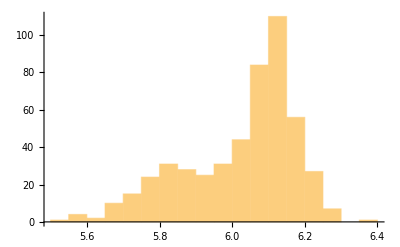

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## CIITensor

-Graphics-

The trimmed mean evaluation time is 0.00004283 seconds

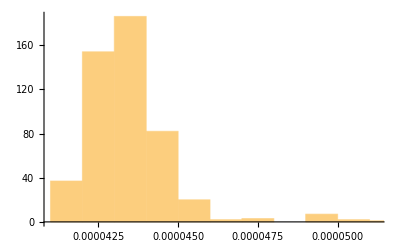

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000779305 seconds

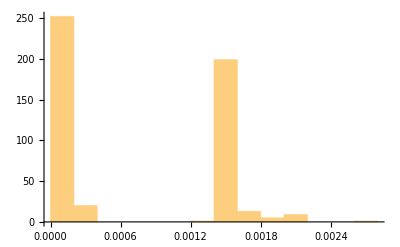

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0017186 seconds

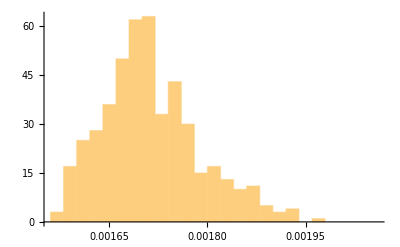

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0267355 seconds

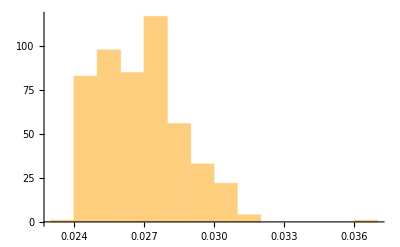

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.51905 seconds

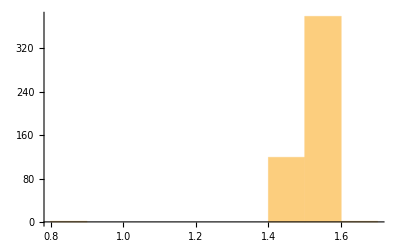

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 12.3006 seconds

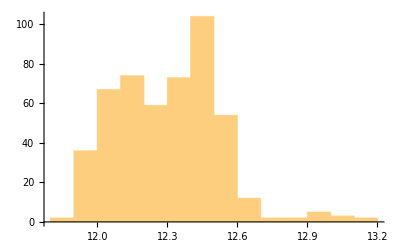

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1,r2,s2,r3,s3,r4,s4,r5,s6}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## CIIITensor

-Graphics-

The trimmed mean evaluation time is 0.00006618 seconds

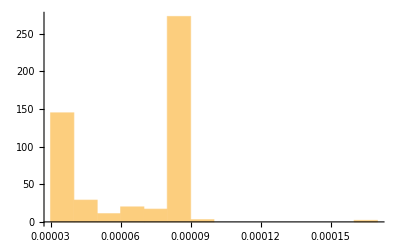

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00055435 seconds

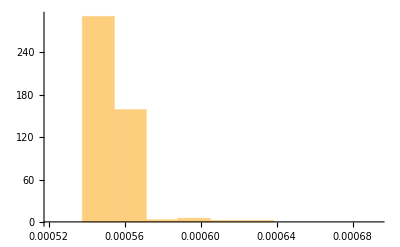

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00337906 seconds

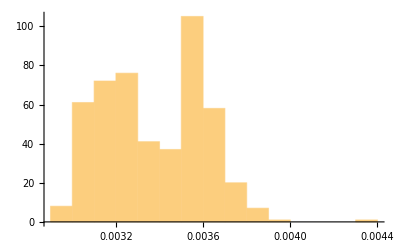

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.05568 seconds

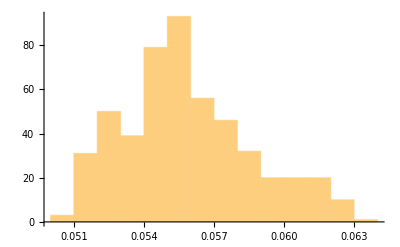

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 2.07093 seconds

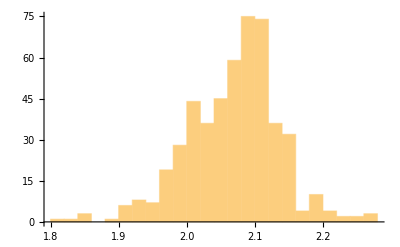

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 26.5256 seconds

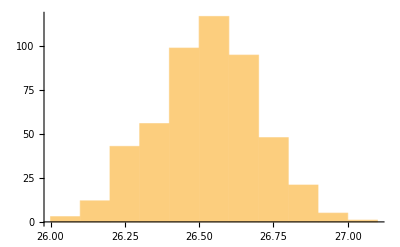

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## CIIIITensor

-Graphics-

The trimmed mean evaluation time is          -6
9.1775 10 seconds

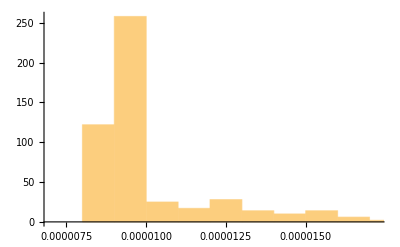

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000192995 seconds

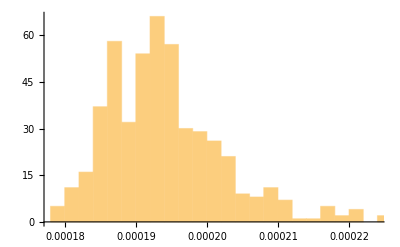

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000450215 seconds

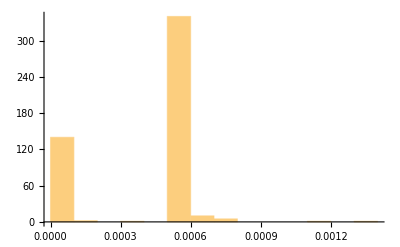

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00068253 seconds

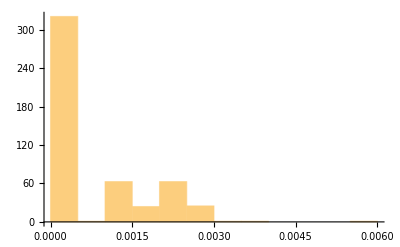

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00153674 seconds

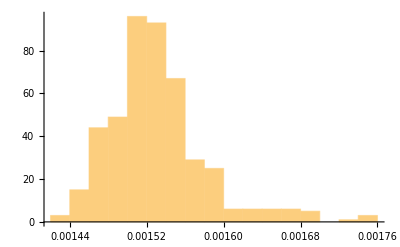

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0148416 seconds

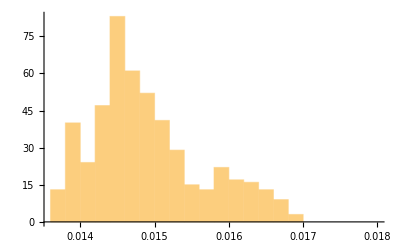

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## ETensor

-Graphics-

The trimmed mean evaluation time is 0.0000123575 seconds

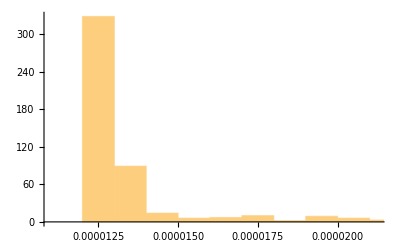

```mathematica
Table[Timing[ETensor[{μ,ν},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000323798 seconds

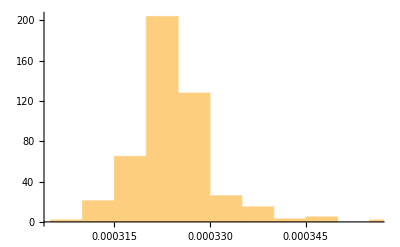

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000627788 seconds

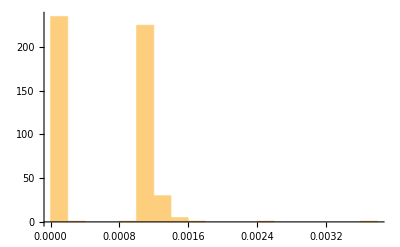

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00092809 seconds

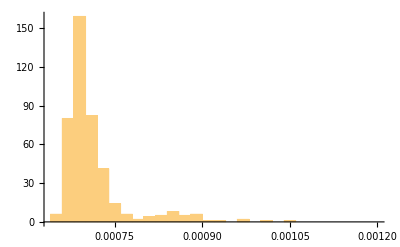

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0059701 seconds

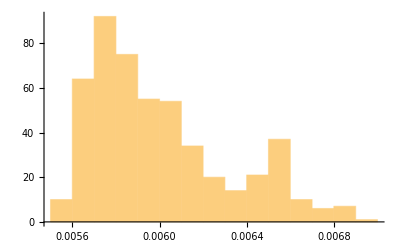

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0650064 seconds

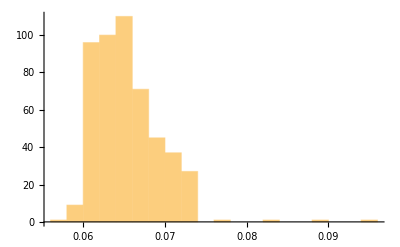

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.917453 seconds

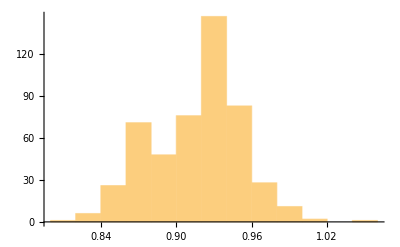

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5,r6,s6}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 14.755 seconds

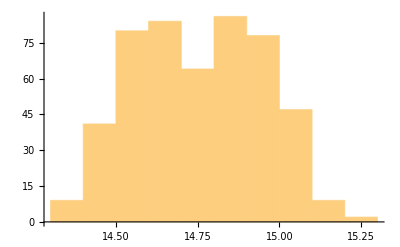

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5,r6,s6,r7,s7}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[];
```

## CETensor

-Graphics-

The trimmed mean evaluation time is 0.000019305 seconds

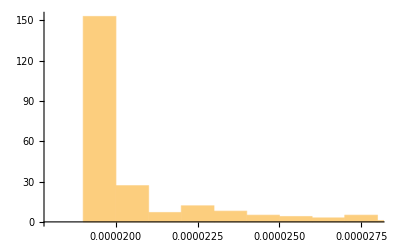

```mathematica
Table[Timing[CETensor[{μ,ν},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00047527 seconds

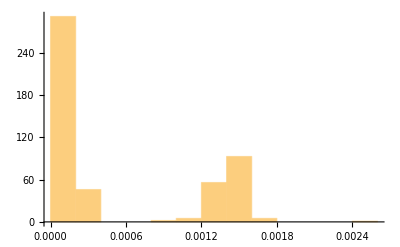

```mathematica
Table[Timing[CETensor[{μ,ν},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000872833 seconds

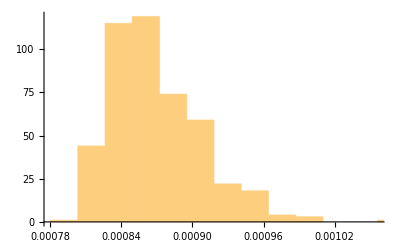

```mathematica
Table[Timing[CETensor[{μ,ν},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0184806 seconds

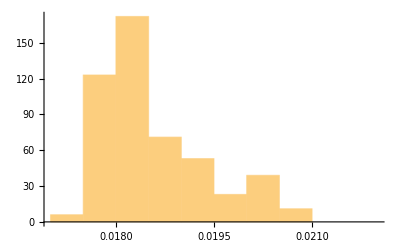

```mathematica
Table[Timing[CETensor[{μ,ν},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.633538 seconds

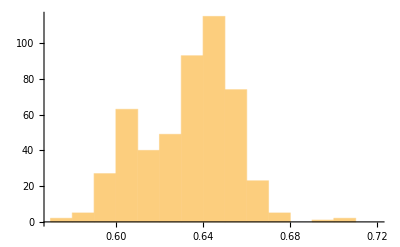

```mathematica
Table[Timing[CETensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

```mathematica
Table[Timing[CETensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

# Scalar-graviton vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## Kinetic term

-Graphics-

The trimmed mean evaluation time is 0.00590128 seconds

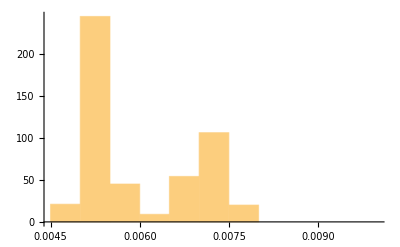

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0251601 seconds

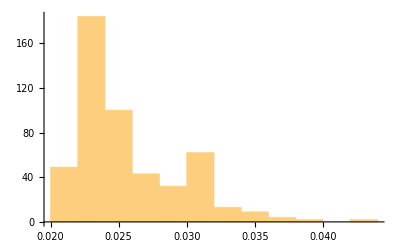

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.24655 seconds

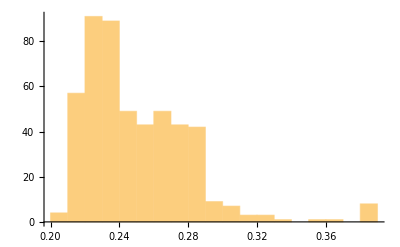

-Graphics-

The trimmed mean evaluation time is 0.222296 seconds

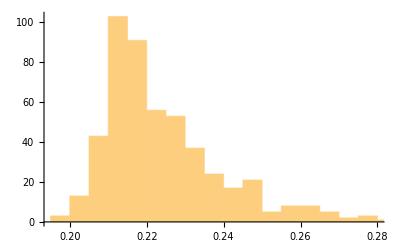

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2,μ3,ν3},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 3.17898 seconds

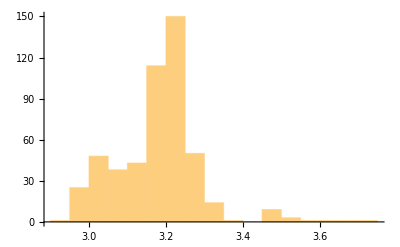

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 53.4722 seconds

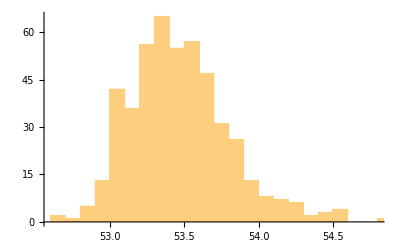

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## Potential term

-Graphics-

The trimmed mean evaluation time is 0.000238965 seconds

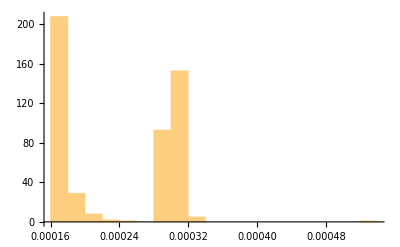

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000955557 seconds

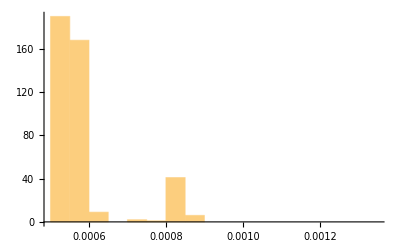

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00526614 seconds

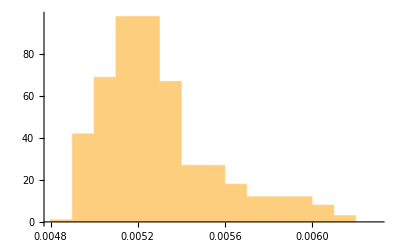

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0937456 seconds

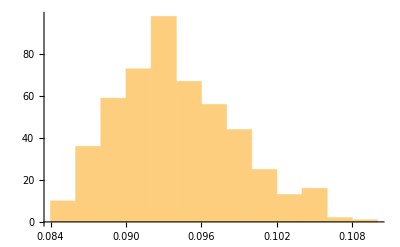

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 2.11334 seconds

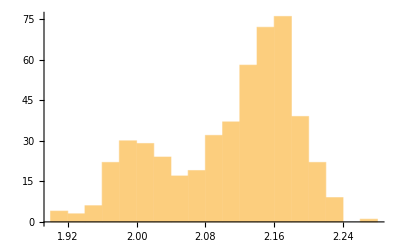

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 58.7965 seconds

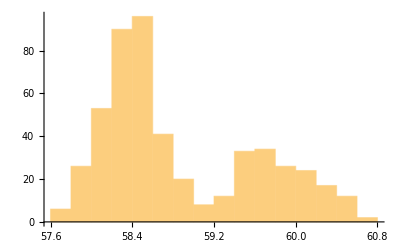

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5,μ6,ν6},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

# Graviton-fermion vertex

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonFermionVertex`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

-Graphics-

The trimmed mean evaluation time is 0.00477402 seconds

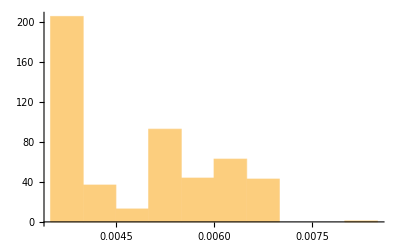

```mathematica
Table[Timing[GravitonFermionVertex[{r1,s1},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0276596 seconds

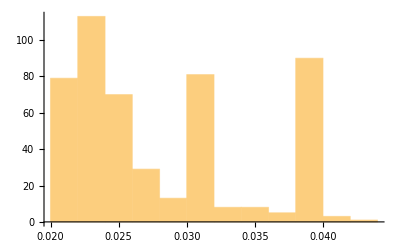

```mathematica
Table[Timing[GravitonFermionVertex[{r1,s1,r2,s2},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

```mathematica
Table[Timing[GravitonFermionVertex[{r1,s1,r2,s2,r3,s3},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.273926 seconds

-Graphics-

```mathematica
Table[Timing[GravitonFermionVertex[{r1,s1,r2,s2,r3,s3,r4,s4},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 3.92486 seconds

-Graphics-

```mathematica
Table[Timing[GravitonFermionVertex[{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

# Graviton-vector vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## Massive vectors

```mathematica
Table[Timing[GravitonMassiveVectorVertex[{μ1,ν1},λ1,p1,λ2,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.023172 seconds

-Graphics-

```mathematica
Table[Timing[GravitonMassiveVectorVertex[{μ1,ν1,μ2,ν2},λ1,p1,λ2,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.166092 seconds

-Graphics-

```mathematica
Table[Timing[GravitonMassiveVectorVertex[{μ1,ν1,μ2,ν2,μ3,ν3},λ1,p1,λ2,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.96503 seconds

-Graphics-

```mathematica
Table[Timing[GravitonMassiveVectorVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},λ1,p1,λ2,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 36.682 seconds

-Graphics-

## Massless vectors

```mathematica
Table[Timing[GravitonVectorVertex[{μ1,ν1,k1},λ1,p1,λ2,p2,ε]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.110937 seconds

-Graphics-

```mathematica
Table[Timing[GravitonVectorVertex[{μ1,ν1,k1,μ2,ν2,k2},λ1,p1,λ2,p2,ε]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.68221 seconds

-Graphics-

```mathematica
Table[Timing[GravitonVectorVertex[{μ1,ν1,k1,μ2,ν2,k2,μ3,ν3,k3},λ1,p1,λ2,p2,ε]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 40.6618 seconds

-Graphics-

## Ghosts

```mathematica
Table[Timing[GravitonVectorGhostVertex[{r1,s1},p1,p2]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00297293 seconds

-Graphics-

```mathematica
Table[Timing[GravitonVectorGhostVertex[{r1,s1,r2,s2},p1,p2]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.018347 seconds

-Graphics-

```mathematica
Table[Timing[GravitonVectorGhostVertex[{r1,s1,r2,s2,r3,s3},p1,p2]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.215183 seconds

-Graphics-

```mathematica
Table[Timing[GravitonVectorGhostVertex[{r1,s1,r2,s2,r3,s3,r4,s4},p1,p2]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 3.17006 seconds

-Graphics-

# Graviton vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

```mathematica
Table[Timing[GravitonVertex[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3},ε]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 5.13667 seconds

-Graphics-

```mathematica
Timing[GravitonVertex[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3},ε]][[1]]
```

5.38848

```mathematica
Timing[GravitonVertex[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3,μ4,ν4,p4},ε]][[1]]
```

194.684

## Graviton-ghost vertex

```mathematica
Table[Timing[GravitonGhostVertex[{m1,n1,k1},λ1,p1,λ2,p2]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0928613 seconds

-Graphics-

```mathematica
Table[Timing[GravitonGhostVertex[{m1,n1,k1,m2,n2,k2},λ1,p1,λ2,p2]][[1]],{n,20}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.22263 seconds

-Graphics-

```mathematica
Table[Timing[GravitonGhostVertex[{m1,n1,k1,m2,n2,k2,m3,n3,k3},λ1,p1,λ2,p2]][[1]],{n,10}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 20.7149 seconds

-Graphics-

```mathematica
Get["../Libs/GravitonGhostVertex_1"]==GravitonGhostVertex[{m1,n1,p1},λ1,k1,λ2,k2]
Get["../Libs/GravitonGhostVertex_2"]==GravitonGhostVertex[{m1,n1,p1,m2,n2,p2},λ1,k1,λ2,k2]
Get["../Libs/GravitonGhostVertex_3"]==GravitonGhostVertex[{m1,n1,p1,m2,n2,p2,m3,n3,p3},λ1,k1,λ2,k2]
```

True

True

True